```mathematica
(*Trapezoidal Quadrature approximation for both dynamics and objective function*)
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
qcontroldattrajopt = Import["trajoptdatx.csv"];
cartpolemantrajopt = Manipulate[
cart = Graphics[{Blue,Rectangle[{x+0,0},{x+2,1}]}, PlotRange->{{-5,5}, {-5, 5}}]/.{x->qcontroldattrajopt[[i]][[1]], ϕ->qcontroldattrajopt[[i]][[2]]};
pole = Graphics[{Thick, Line[{{x+1,1/2},{x+1-3*Sin[ϕ],1/2+3*Cos[ϕ]}}]}]/.{x->qcontroldattrajopt[[i]][[1]], ϕ->qcontroldattrajopt[[i]][[2]]};
Show[cart, pole]
,{i, 1, Length[qcontroldattrajopt], 1}]
```

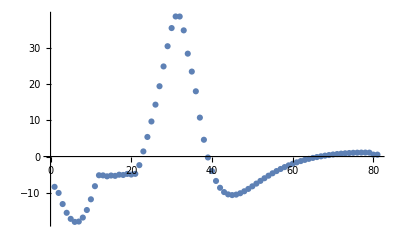

```mathematica
controldat = Import["trajoptdatu.csv"];
ListPlot[Flatten[controldat], PlotRange->All]
```

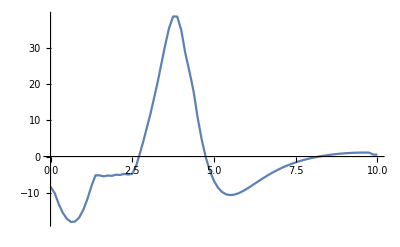

```mathematica
Plot[uinter[t],{t, 0, 10}]
```

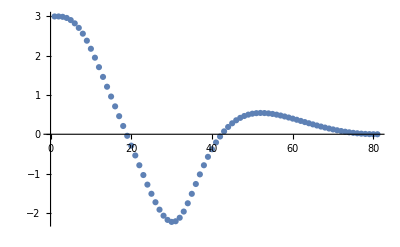

```mathematica
ListPlot[qcontroldattrajopt[[;;, 1]], PlotRange->All]
```

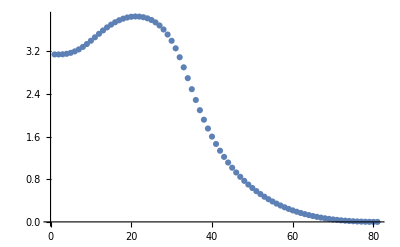

```mathematica
ListPlot[qcontroldattrajopt[[;;, 2]], PlotRange->All]
```

```mathematica
(*So these are the soltions obtained at the collocation points of the transcription. Now we need to interpolate these solutions*)
```

```mathematica
(*Interpolation*)
```

Control input was assumed to be linear in nature and hence will be its interpolation as,
β = (-1/h) * (u(k) - u(k-1))
u(t) = u(k) + δ(k) β
where δk = t - tk

Where as since the dynamics was assumed to be linear, the state approximation would be quadratic
γk = -1/(2*h) * (f(k) - f(k+1))
x(t) = x(k) + δk * f(k) + δk^2 *γk

```mathematica
(*Verifying the solution accuracy*)
```

```mathematica
(*We need to interpolate and then use the original dynamics equations to find the difference between these and plot them. Also After we get to this stage, we should check for the h-convergence.*)
```

```mathematica
(*Validating dynamics to see if it actually works in sim*)
```

```mathematica
(*System information*)
```

```mathematica
data = {M->2, m->1, l->3, g->9.81};
```

```mathematica
(*Lagrangian Dynamics Formulation*)
```

```mathematica
KE = Simplify[Expand[1/2*(M*x'[t]^2+m*((D[x[t]-l*Sin[θ[t]], t]^2)+D[l*Cos[θ[t]], t]^2))]];
PE = m*g*l*Cos[θ[t]];
Lagrangian = KE-PE;
```

```mathematica
eq1 = Simplify[D[D[Lagrangian, x'[t]],t]-D[Lagrangian, x[t]]-fcart];
eq2 = Simplify[D[D[Lagrangian, θ'[t]],t]-D[Lagrangian, θ[t]]];
dyn = {x''[t], θ''[t]}/.Solve[{eq1==0, eq2==0}, {x''[t], θ''[t]}][[1]];
dyneqns = Simplify[dyn/.data];
```

```mathematica
(*The systems configuration space belongs to R^1 X S^1*)
```

```mathematica
q = {x, θ};
```

```mathematica
(*Leaving the system with an initial condition and simulating it to see if the dynamics is correct*)
```

```mathematica
(*Initial conditions*)
```

```mathematica
qinit ={0,π/4};
dqinit = {-0.05, 0};
```

```mathematica
(*qinit ={0,0+0.0000001};
dqinit = {0, 0};*)
```

```mathematica
dyntesteqns = dyneqns/.fcart->0;
```

```mathematica
dyntest = NDSolve[{dyntesteqns[[1]]==x''[t], dyntesteqns[[2]]==θ''[t], {x[0], θ[0]}== qinit, {x'[0], θ'[0]}==dqinit},q,{t, 0, 10}, AccuracyGoal->15, Method->"Adams"][[1]]
```

{x→InterpolatingFunction[…],θ→InterpolatingFunction[…]}

```mathematica
(*Plotting the trajectories*)
```

```mathematica
θplottest = Plot[(θ/.dyntest[[2]])[t], {t, 0, 10}, PlotStyle->Green];
xplottest = Plot[( x/.dyntest[[1]])[t], {t, 0, 10}];
Show[θplottest, xplottest];
```

```mathematica
(*Checking the energy*)
```

```mathematica
Energyexp = (KE+PE)/.data;
```

```mathematica
(*Discretising the solutions*)
```

```mathematica
qtestdat = Table[{(x/.dyntest[[1]])[t], (θ/.dyntest[[2]])[t], (x/.dyntest[[1]])'[t], (θ/.dyntest[[2]])'[t]},{t, 0, 10, 0.01}];
time = Table[t, {t, 0, 10, 0.01}];
```

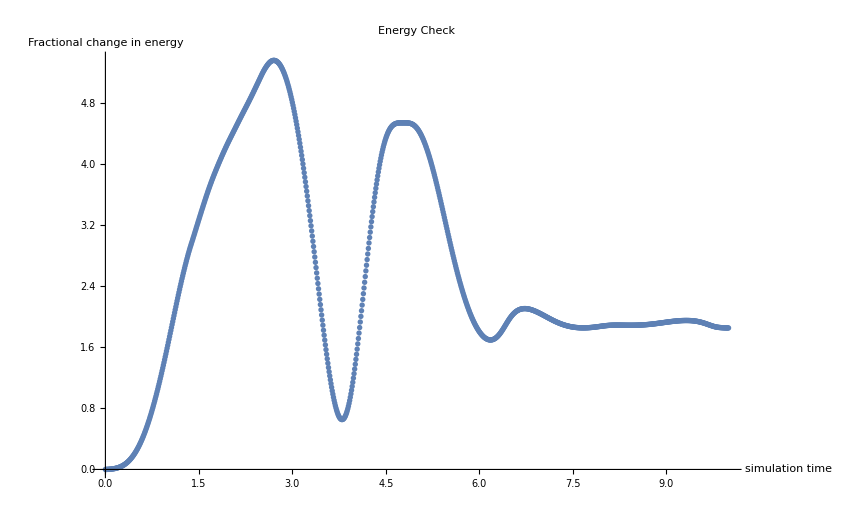

```mathematica
Energytestdat = Table[Energyexp/.Inner[Rule, {x[t], θ[t], x'[t], θ'[t]}, qtestdat[[i]], List], {i, Length[qtestdat]}];
E1 = ConstantArray[Energytestdat[[1]], Dimensions[Energytestdat]];
ListPlot[Transpose[{time, (Energytestdat-E1)/E1}], PlotLabel->"Energy Check", AxesLabel->{"simulation time", "Fractional change in energy"}]
```

```mathematica
(*The mathematical model is consistent*)
```

```mathematica
(*Visualisation*)
```

```mathematica
Manipulate[
cart = Graphics[{Orange,Rectangle[{x+0,0},{x+2,1}]}, PlotRange->{{-4, 4}, {-4, 4}}]/.{x->qtestdat[[i]][[1]], ϕ->qtestdat[[i]][[2]]};
pole = Graphics[{Black, Thick, Line[{{x+1,1/2},{x+1-3*Sin[ϕ],1/2+3*Cos[ϕ]}}]}]/.{x->qtestdat[[i]][[1]], ϕ->qtestdat[[i]][[2]]};
Show[cart, pole]
,{i, 1, Length[qtestdat], 1}]
```

```mathematica
(*Interpolating the controller*)
tf = 5;
uvals = Table[Join[{(i-1)*tf/(Length[controldat]-1)}, Flatten[controldat[[i]]]], {i, Length[controldat]}];
uinter = Interpolation[uvals, InterpolationOrder->1];
```

```mathematica
controller[t_] := Module[{},
Return[{-(uinter[t]+4.905 Sin[2 θ[t]]-3 Sin[θ[t]] θ'[t]^2)/(-3+Cos[θ[t]]^2),(-0.3333333333333333 *uinter[t]* Cos[θ[t]]-9.809999999999999 Sin[θ[t]]+0.5 Sin[2 θ[t]] θ'[t]^2)/(-3.+Cos[θ[t]]^2)}];
]
```

```mathematica
controlsim = NDSolve[{controller[t]=={x''[t], θ''[t]}, {x[0], θ[0]}== qcontroldattrajopt[[1]][[;;2]], {x'[0], θ'[0]}=={0,0}},q,{t, 0, 5}, AccuracyGoal->15, Method->"Adams"][[1]]
```

{x→InterpolatingFunction[…],θ→InterpolatingFunction[…]}

```mathematica
(*Plotting the trajectories*)
```

```mathematica
θplottest = Plot[(θ/.controlsim[[2]])[t], {t, 0, 10}, PlotStyle->Green];
xplottest = Plot[( x/.controlsim[[1]])[t], {t, 0, 10}];
Show[θplottest, xplottest];
```

```mathematica
(*Discretising the solutions*)
```

```mathematica
qtestdat = Table[{(x/.controlsim[[1]])[t], (θ/.controlsim[[2]])[t], (x/.controlsim[[1]])'[t], (θ/.controlsim[[2]])'[t]},{t, 0, tf, 0.01}];
time = Table[t, {t, 0, tf, 0.01}];
```

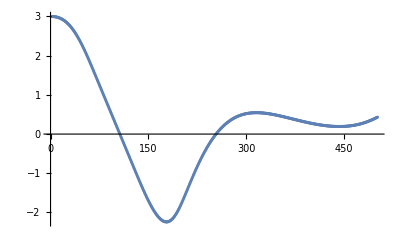

```mathematica
ListPlot[qtestdat[[;;,1]]]
```

```mathematica
Manipulate[
cart = Graphics[{Orange,Rectangle[{x+0,0},{x+2,1}]}, PlotRange->{{-5, 5}, {-5, 5}}]/.{x->qtestdat[[i]][[1]], ϕ->qtestdat[[i]][[2]]};
pole = Graphics[{Black, Thick, Line[{{x+1,1/2},{x+1-3*Sin[ϕ],1/2+3*Cos[ϕ]}}]}]/.{x->qtestdat[[i]][[1]], ϕ->qtestdat[[i]][[2]]};
Show[cart, pole]
,{i, 1, Length[qtestdat], 1}]
```